# QNMs of a Kerr Black Hole

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Basic definitions *)
Δ[r_]:=r^2+a^2-2M r;
rp=M+√(M^2-a^2);
rm=M-√(M^2-a^2);
```

```mathematica
a=χ M;
```

```mathematica
s=-2; (* gravitational perturbation *)
l=2; (* most significant values for GWs *)
m=2;
```

## Slow-rotation Limit

```mathematica
Simplify[Series[rp,{χ,0,0}],M>0]
```

2 M+O[χ]^1

## Computing the QNMs

```mathematica
f[r_]:=1-(2 M)/r;
```

```mathematica
rs[r_]:=Simplify[Integrate[1/f[r],r],r>2M>0];
V1=f[r]((l(l+1))/r^2 -(6 M)/r^3+(24 m χ M^2(3r-7 M))/(l(l+1)ω r^6));
EQ1=f[r]^2 ψ''[r]+f'[r]f[r]ψ'[r]+(ω^2-(4 m χ M^2 ω)/r^3-V1)ψ[r]
```

(-((1-(2 M)/r) (-(6 M)/r^3+6/r^2+(8 M^2 (-7 M+3 r) χ)/(r^6 ω)))-(8 M^2 χ ω)/r^3+ω^2) ψ[r]+(2 M (1-(2 M)/r) ψ'[r])/r^2+(1-(2 M)/r)^2 ψ''[r]

### Expansion at the horizon

```mathematica
(* Expand EQ using ψ=(r-r_+)^(-2MⅈΩ[r_+])h[r] (da dove esce fuori ?)  in the limit r_+ -> 2M *)
Ω=√(ω^2-(4 m χ M^2 ω)/(2 M)^3);
ϕ[r_]:=(r-2 M)^(-2 M ⅈ Ω)h[r];
sHor=Simplify[EQ1/.{ψ[r]->ϕ[r],ψ'[r]->ϕ'[r],ψ''[r]->ϕ''[r]}]
```

1/(r^7 ω)(-2 M+r)^(1-2 ⅈ M √(ω (-χ/M+ω))) ((56 M^3 χ-24 M^2 r χ+r^4 ω (-6+r^2 ω^2)+2 M r^3 ω (3+2 r χ ω+r^2 ω^2+ⅈ r √(ω (-χ/M+ω)))) h[r]+r^4 ω (M (2-4 ⅈ r √(ω (-χ/M+ω))) h'[r]+r (-2 M+r) h''[r]))

```mathematica
(* Series coefficients *)
CoefHor[ord_]:=Module[{H,CT,s1,s2},
H[r_]:=Sum[hHor[i](r-2 M)^i,{i,0,ord+5}];
CT=l(l+1)r^7 ω(r-2 M)^(2 M ⅈ Ω-1);(* inverse of the common term *)
s1=Simplify[Normal[Series[CT×sHor,{χ,0,1}]]];
s2=Simplify[Series[s1/.{h[r]->H[r],h'[r]->D[H[r],r],h''[r]->D[H[r],{r,2}]},{r,2 M,ord}],ω>0];

(* Solve the system *)
Simplify[Solve[Table[SeriesCoefficient[s2,i]==0,{i,0,ord}],Table[hHor[i],{i,1,ord+1}]]]
]
```

```mathematica
ordHor=10;(* NOTE: the last coefficient is one order higher *)
coefHor=CoefHor[ordHor][[1]];
```

```mathematica
Export["CoefHor_Kerr_SR.m",coefHor]
```

CoefHor_Schw.m

### Expansion at infinity

```mathematica
(*Expand EQ using ψ=e^ⅈωz[r] g[r] and z[r]=r_*. At infinity Ω -> ω*)
ϕ[r_]:=Exp[ⅈ ω z[r]]g[r];
s=Simplify[EQ1/.{ψ[r]->ϕ[r],ψ'[r]->ϕ'[r],ψ''[r]->ϕ''[r]}];
sInf=Simplify[s/.{z[r]->rs[r],z'[r]->D[rs[r],r],z''[r]->D[rs[r],{r,2}]}]
```

1/(l (1+l) r^7 ω)ⅇ^(ⅈ ω (r+2 M Log[-2 M+r])) ((l (1+l) (2 M-r) r^3 (-6 M+l (1+l) r) ω-4 m M^2 χ (84 M^2-78 M r+18 r^2+l r^4 ω^2+l^2 r^4 ω^2)) g[r]-l (1+l) (2 M-r) r^4 ω (2 (M+ⅈ r^2 ω) g'[r]+r (-2 M+r) g''[r]))

```mathematica
(* Series coefficients *)
CoefInf[ord_]:=Module[{G,CT,s1,s2},
G[r_]:=Sum[gInf[i]/r^i,{i,0,ord+5}];
CT=Exp[-ⅈ ω rs[r]];(* inverse of the common term *)
s1=Simplify[Normal[Series[CT×sInf,{χ,0,1}]]];
s2=Simplify[Series[s1/.{g[r]->G[r],g'[r]->G'[r],g''[r]->G''[r]},{r,∞,ord}],ω>0];

(* Solve the system *)
Simplify[Solve[Table[SeriesCoefficient[s2,i]==0,{i,2,ord}],Table[gInf[i],{i,1,ord-1}]]]
]
```

```mathematica
ordInf=10;(* NOTE: the last coefficient is one order lower *)
coefInf=CoefInf[ordInf][[1]];
```

```mathematica
Export["CoefInf_Kerr_SR.m",coefInf]
```

CoefInf_Schw.m

### QNM finder

```mathematica
coefHor=Import["CoeffHor_Kerr.m"];
coefInf=Import["CoeffInf_Kerr.m"];
```

```mathematica
(* Integrator V2.5 *)
IntQNM[ω0_,χ0_,value_,coefHor_,coefInf_]:=Module[{rules,param,prec,rHor,rm,rInf,ξ,ξHor,ξInf,EQs,BCs,ordHor,ordInf},
rules={AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->20};(*,Method->"StiffnessSwitching"*)

param=Union[{M->1,ω->ω0,χ->χ0,hHor[0]->1,gInf[0]->1},Thread[{eps,match,inf}->value]];
prec=Max[20,Min[Precision[#]&/@param]];param=SetPrecision[#,prec]&/@param;

rHor=2M(1+eps)/.param;
rm=match×M/.param;
rInf=inf×M/.param;

EQs=SetPrecision[{EQ1==0}//.Union[param,{ψ[r]->ξ[r],ψ'[r]->ξ'[r],ψ''[r]->ξ''[r]}],prec];

(* Solution integrating from the horizon *)
ordHor=Length[coefHor];
ξHor=(r-2M)^(-2 ⅈ Ω M)Sum[hHor[i] (r-2M)^i,{i,0,ordHor}]//.Union[param,coefHor];
BC1=SetPrecision[ξHor/.r->rHor,prec];BC2=SetPrecision[D[ξHor,r]/.r->rHor,prec];
BCs={ξ[rHor]==BC1,ξ'[rHor]==BC2};

ψHor=ξ[r]/.NDSolve[Union[EQs,BCs],ξ,{r,rHor,rm},rules][[1]];

(* Solution integration from infinity *)
ordInf=Length[coefInf];
ξInf=Exp[ⅈ ω rs[r]]Sum[gInf[i]/r^i,{i,0,ordInf}]//.Union[param,coefInf];
BC1=SetPrecision[ξInf/.r->rInf,prec];BC2=SetPrecision[D[ξInf,r]/.r->rInf,prec];
BCs={ξ[rInf]==BC1,ξ'[rInf]==BC2};

ψInf=ξ[r]/.NDSolve[Union[EQs,BCs],ξ,{r,rInf,rm},rules];

(*Linear combination*)
b=ψHor/ψInf/.r->rm;(* we fix the coefficients of the linear combination in order for ψn to be continuous at r=rm *)
ψn=Piecewise[{{ψHor,r<rm},{b×ψInf,r≥rm}}];
Δψp=(D[ψHor,r]-D[b ψInf,r])/D[ψHor,r]/.r->rm;
{Δψp}
]
```

```mathematica
FindQNM[ωguess_,χ0_]:=Module[{gg},
gg[xx_?NumericQ]:=IntQNM[xx,χ0,{10^-4,10,50},coefHor,coefInf][[1]];
root=xx/.FindRoot[gg[xx]==0,{xx,ωguess},AccuracyGoal->6,WorkingPrecision->20][[1]];
check=Abs[gg[root]];
{root,check}
]
```

```mathematica
FindQNM[0.4-0.1ⅈ,0]
```

{0.37367165566648803794-0.088962274342542433442 ⅈ,{6.×10^-16}}

## Numerical Stability

### Parameters

### Spin

```mathematica
χarray={10^-2,5 10^-2,10^-1,15 10^-2,2 10^-1,25 10^-2,3 10^-1};
ωtrue={0.3749365685-0.08894183057ⅈ,0.3801455748-0.08884890191ⅈ,0.3870175384-0.08870569903ⅈ,0.3943329877-0.08852826817ⅈ,0.4021453242-0.08831116621ⅈ,0.4105179098-0.08804765025ⅈ,0.4195266818-0.08772927189ⅈ};
(*ωguess={};*)
```

```mathematica
ωfound={};
ωguess=0.4-0.1 ⅈ;
Monitor[Do[
AppendTo[ωfound,FindQNM[ωguess,χarray[[i]]][[1]]];ωguess=ωfound[[-1]],{i,1,Length[χarray]}
],ωfound]
```

```mathematica
Export["QNM_Kerr.dat",ωfound]
```

QNM_Kerr.dat

```mathematica
ωimport=Import["QNM_Kerr.dat"]//ToExpression;
ωimport[[All,1]]
```

{0.37493554896013548915-0.088940225828060576262 ⅈ,0.38011468480976865402-0.088796880876980468325 ⅈ,0.38688390255800368524-0.088461317888082946707 ⅈ,0.39400536021058713884-0.087879191178278778393 ⅈ,0.40149955509578304325-0.086934699878969150169 ⅈ,0.40936846940174535015-0.085441170610347019886 ⅈ,0.41756552166195877733-0.083073773355454963605 ⅈ}

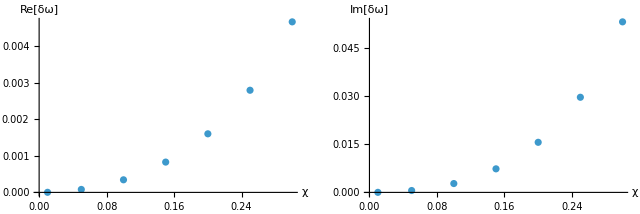

```mathematica
ΔωR=Abs[(Re[ωimport[[All,1]]]-Re[ωtrue])/Re[ωtrue]];(* Table[ωfound[[i]]-ωtrue[[i]],{i,1,size}]; *)
ΔωI=Abs[(Im[ωimport[[All,1]]]-Im[ωtrue])/Im[ωtrue]];
dataR=Transpose@{χarray,ΔωR};
dataI=Transpose@{χarray,ΔωI};

GraphicsRow[{ListPlot[dataR,AxesLabel->{"χ","Re[δω]"}],ListPlot[dataI,AxesLabel->{"χ","Im[δω]"}]}](* ,ScalingFunctions->{None,"Log"} *)
```

```mathematica
(* con ordHor=3
1.403173173208927*^-7-2.594252477838843*^-7 ⅈ,1.3839418633310174*^-7-2.5434630081255793*^-7 ⅈ,1.305543594343206*^-7-2.399207012504512*^-7 ⅈ *)
```

```mathematica
(* con ordHor=7
1.403173173208927*^-7-2.594252477838843*^-7 ⅈ,1.3839418633310174*^-7-2.5434630081255793*^-7 ⅈ,1.305543594343206*^-7-2.399207012504512*^-7 ⅈ *)
```

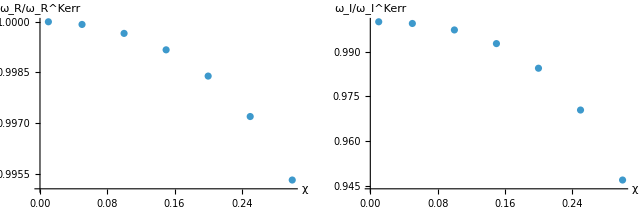

```mathematica
(*ωR=Re[ωimport[[All,1]]]/Re[ωtrue];(* Table[ωfound[[i]]-ωtrue[[i]],{i,1,size}]; *)
ωI=Im[ωimport[[All,1]]]/Im[ωtrue];*)
ωR=Re[ωfound]/Re[ωtrue];(* Table[ωfound[[i]]-ωtrue[[i]],{i,1,size}]; *)
ωI=Im[ωfound]/Im[ωtrue];
dataR=Transpose@{χarray,ωR};
dataI=Transpose@{χarray,ωI};

GraphicsRow[{ListPlot[dataR,AxesLabel->{"χ","ω_R/ω_R^Kerr"}],ListPlot[dataI,AxesLabel->{"χ","ω_I/ω_I^Kerr"}]}](* ,ScalingFunctions->{None,"Log"} *)
```

## General Case

### Set-up

```mathematica
(* Tortoise coordinate *)
rs[r_]:=Simplify[Integrate[(r^2+a^2)/((r-r1)(r-r2)),r]/.{r1->rp,r2->rm},{r>rp>rm>0,a>0}];

(* Potential from Eq. 4.2 of https://arxiv.org/pdf/0808.1615*)
K=(r^2+a^2)ω-a m;G=(s(r-M))/(r^2+a^2)+(r Δ[r])/((r^2+a^2)^2);
V2=Simplify[(K^2-2ⅈ s(r-M)K+Δ[r](4ⅈ s ω r-Λ))/((r^2+a^2)^2)-G^2-Δ[r]/(r^2+a^2)D[G,r]];(* where the last term is dG/dr_* in terms of r *)
EQ2=(Δ[r]/(r^2+a^2))^2 Y''[r]+Δ[r]/(r^2+a^2)D[Δ[r]/(r^2+a^2),r]Y'[r]+V2 Y[r];(* where Y[r]=Δ^(s/2)(r^2+a^2)^(1/2)R[r] *)
```

```mathematica
Print["Tortoise coordinate r_* = ", rs[r],"\t and (dr_*)/dr= ",D[rs[r],r]//Simplify];
Print["Teukolsky equation:\n",EQ2," = 0"];
```

Tortoise coordinate r_* = r+(M-M/(√(1-χ^2))) Log[r+M (-1+√(1-χ^2))]+M (1+1/(√(1-χ^2))) Log[r-M (1+√(1-χ^2))]	 and (dr_*)/dr= (r^2+M^2 χ^2)/(-2 M r+r^2+M^2 χ^2)

Teukolsky equation:
-1/((r^2+M^2 χ^2)^4)((r^3 (1+s)-M r^2 (2+s)-M^3 s χ^2+M^2 r (1+s) χ^2)^2+(-2 M r+r^2+M^2 χ^2) (-r^4 (1+s)+2 M r^3 (2+s)+2 M^3 r (-2+s) χ^2+M^4 (1+s) χ^4)-(r^2+M^2 χ^2)^2 ((-2 M r+r^2+M^2 χ^2) (-Λ+4 ⅈ r s ω)+(m M χ-(r^2+M^2 χ^2) ω)^2+2 ⅈ (M-r) s (-m M χ+(r^2+M^2 χ^2) ω))) Y[r]+((-2 M r+r^2+M^2 χ^2) ((-2 M+2 r)/(r^2+M^2 χ^2)-(2 r (-2 M r+r^2+M^2 χ^2))/((r^2+M^2 χ^2)^2)) Y'[r])/(r^2+M^2 χ^2)+((-2 M r+r^2+M^2 χ^2)^2 Y''[r])/((r^2+M^2 χ^2)^2) = 0

### Angular eigenvalues

```mathematica
ap=Max[Abs[m],Abs[s]];am=(m s)/Max[Abs[m],Abs[s]];
h[l_]:=((l^2-ap^2)(l^2-am^2)(l^2-s^2))/(2(l-1/2)l^3(l+1/2));
fslm={l(l+1)−s(s+1),−2(m s^2)/(l(l+1)),h[l+1]−h[l]−1};(* see Eqs. 2.16 of https://arxiv.org/pdf/gr-qc/0511111 *)
Aslm=Simplify[Sum[fslm[[n]](a ω)^(n-1),{n,1,3}]];(* angular eigenvalues in the limit aω << 1 *)
λ=Aslm+(a ω)^2-2a ω m;
```

## Computing the QNMs

### Expansion at the horizon

```mathematica
Ω=a/(2M rp);
k=ω-m Ω;(* frequency near the horizon *)
```

```mathematica
Yhor[r_]:=Δ[r]^(s/2)(r^2+a^2)^(1/2)Δ[r]^-s Exp[-ⅈ k rs[r]];(* se la superficie è poco fuori l'orizzonte posso usare somma di entrante e uscente *)
Simplify[Series[Yhor[r],{r,rp,0}],{M>0,a>0}]
```

(-√(-a^2+M^2) (M+√(-a^2+M^2)-r))^(-s/2) (-M-√(-a^2+M^2)+r)^((ⅈ (a m-2 M (M+√(-a^2+M^2)) ω))/(2 √(-a^2+M^2))) (2^(1/2-s/2+(ⅈ a (m (-M+√(-a^2+M^2))+2 a M ω))/(-2 a^2+2 M (M+√(-a^2+M^2)))) ⅇ^(-(ⅈ (a^3 m-a m M (M+√(-a^2+M^2))+4 M^3 (M+√(-a^2+M^2)) ω-2 a^2 M (2 M+√(-a^2+M^2)) ω))/(2 M (-a^2+M (M+√(-a^2+M^2))))) (-a^2+M^2)^((ⅈ a (m (-M+√(-a^2+M^2))+2 a M ω))/(-4 a^2+4 M (M+√(-a^2+M^2)))) √(M (M+√(-a^2+M^2)))+O[r-M-√(-a^2+M^2)]^1)

```mathematica
ϕHor[r_]:=Exp[-ⅈ k rs[r]] Δ[r]^(-s/2)𝕙[r];
CT=Exp[-ⅈ k rs[r]] Δ[r]^(-s/2);
sHor=Simplify[EQ2/CT/.{Y[r]->ϕHor[r],Y'[r]->ϕHor'[r],Y''[r]->ϕHor''[r]},{M>0,a>0}];
```

-1/((a^2+r^2)^4)(2 (M-r)^2 (a^2+r^2)^2 s η[r]-2 r (-M+r) (a^2+r^2) (a^2+r (-2 M+r)) s η[r]+(a^2+r^2)^2 (a^2+r (-2 M+r)) s η[r]-(M-r)^2 (a^2+r^2)^2 s (2+s) η[r]+(a^2+r (-2 M+r)) (2 a^2 M r (-2+s)+a^4 (1+s)-r^4 (1+s)+2 M r^3 (2+s)) η[r]+(a^2 (r-M s+r s)+r^2 (r (1+s)-M (2+s)))^2 η[r]-(ⅈ (a^2-r^2) (a^2+r^2)^2 (a m-2 M (M+√(-a^2+M^2)) ω) η[r])/(M+√(-a^2+M^2))+(ⅈ r (a^2+r^2)^2 (a^2+r (-2 M+r))^2 (a m-2 M (M+√(-a^2+M^2)) ω) η[r])/(M (M+√(-a^2+M^2)) (M-√(-a^2+M^2)-r) (M+√(-a^2+M^2)-r))+((a^2+r^2)^4 (a^2+r (-2 M+r))^2 (a m-2 M (M+√(-a^2+M^2)) ω)^2 η[r])/(4 M^2 (M+√(-a^2+M^2))^2 (M+√(-a^2+M^2)-r)^2 (-M+√(-a^2+M^2)+r)^2)+(ⅈ (M-r) (-a^2+(2 M-r) r) (a^2+r^2)^3 (-a m+2 M (M+√(-a^2+M^2)) ω) η[r])/(M (M+√(-a^2+M^2)) (M-√(-a^2+M^2)-r) (M+√(-a^2+M^2)-r))-(ⅈ (M-r) (-a^2+(2 M-r) r) (a^2+r^2)^3 s (-a m+2 M (M+√(-a^2+M^2)) ω) η[r])/(M (M+√(-a^2+M^2)) (M-√(-a^2+M^2)-r) (M+√(-a^2+M^2)-r))+(a^2+r^2)^2 (-(a m-(a^2+r^2) ω)^2+2 ⅈ (-M+r) s (-a m+(a^2+r^2) ω)+(a^2+r (-2 M+r)) (Λ-4 ⅈ r s ω)) η[r]-(-2 M+2 r) (a^2+r^2)^2 (a^2+r (-2 M+r)) η'[r]+2 r (a^2+r^2) (a^2+r (-2 M+r))^2 η'[r]+(-2 M+2 r) (a^2+r^2)^2 (a^2+r (-2 M+r)) s η'[r]-(ⅈ (a^2+r^2)^3 (a^2+r (-2 M+r))^2 (a m-2 M (M+√(-a^2+M^2)) ω) η'[r])/(M (M+√(-a^2+M^2)) (M-√(-a^2+M^2)-r) (M+√(-a^2+M^2)-r))-(a^2+r^2)^2 (a^2+r (-2 M+r))^2 η''[r])

```mathematica
(* Series coefficients *)
CoefHor[ord_]:=Module[{H,s},
H[r_]:=Sum[hHor[i](r-rp)^i,{i,0,ord+5}];
s=Simplify[Series[sHor/.{𝕙[r]->H[r],𝕙'[r]->D[H[r],r],𝕙''[r]->D[H[r],{r,2}]},{r,rp,ord}],{M>0,a>0}];

(* Solve the system *)
Simplify[Solve[Table[SeriesCoefficient[s,i]==0,{i,0,ord}],Table[hHor[i],{i,1,ord}]]]
]
```

```mathematica
ordHor=4;(* NOTE: the last coefficient is one order higher *)
coefHor=CoefHor[ordHor][[1]];
```

```mathematica
Export["CoefHor_4_Kerr.m",coefHor]
```

CoefHor_4_Kerr.m

### Expansion at infinity

```mathematica
Yinf[r_]:=Δ[r]^(s/2)(r^2+a^2)^(1/2)Exp[ⅈ ω rs[r]]/r^(2s+1);
Simplify[Series[Yinf[r],{r,∞,0}],{M>0,a>0}]
```

ⅇ^(ⅈ ω r+2 ⅈ M ω Log[r]-(4 ⅈ M^2 ω)/r+O[1/r]^2) r^(-2 s) (a^2+r (-2 M+r))^(s/2) (1+O[1/r]^2)

```mathematica
ϕInf[r_]:=Exp[ⅈ ω rs[r]] r^-s 𝕘[r];
CT=Exp[ⅈ ω rs[r]] r^-s;
sInf=Simplify[EQ2/CT/.{Y[r]->ϕInf[r],Y'[r]->ϕInf'[r],Y''[r]->ϕInf''[r]},{M>0,a>0}];
```

1/(r^2 (a^2+r^2)^4)((-2 a^7 m r^2 ω+a^8 s (1+s-2 ⅈ r ω)-2 a m r^6 (ⅈ M s+r (-ⅈ s+r ω))-2 a^5 m r^2 (ⅈ M s+r (-ⅈ s+3 r ω))-2 a^3 m r^4 (2 ⅈ M s+r (-2 ⅈ s+3 r ω))+a^6 r (-2 M s (1+2 s)-6 ⅈ r^2 s ω+r (-1+m^2+3 s+4 s^2-Λ+6 ⅈ M s ω))+r^6 (M^2 (4+8 s+3 s^2)-r^2 Λ+2 M r (-1-2 s-s^2+Λ-ⅈ r s ω))+a^2 r^4 (M^2 (-8+8 s+6 s^2)+2 M r (2-5 s-4 s^2+2 Λ+ⅈ r s ω)+r^2 (-1+m^2+s+2 s^2-3 Λ-2 ⅈ r s ω))+a^4 r^2 (3 M^2 s^2+2 M r (3-4 s-5 s^2+Λ+5 ⅈ r s ω)+r^2 (-2+2 m^2+3 s+5 s^2-3 Λ-6 ⅈ r s ω))) γ[r]+r (a^2+r^2) (a^2+r (-2 M+r)) (2 (-a^4 (s-ⅈ r ω)+r^3 (M+2 M s-r s+ⅈ r^2 ω)+a^2 r (-M+2 M s-2 r s+2 ⅈ r^2 ω)) γ'[r]+r (a^2+r^2) (a^2+r (-2 M+r)) γ''[r]))

```mathematica
(* Series coefficients *)
CoefInf[ord_]:=Module[{G,s},
G[r_]:=Sum[gInf[i]/r^i,{i,0,ord+5}];
s=Simplify[Series[sInf/.{𝕘[r]->G[r],𝕘'[r]->D[G[r],r],𝕘''[r]->D[G[r],{r,2}]},{r,∞,ord}],{M>0,a>0}];

(* Solve the system *)
Simplify[Solve[Table[SeriesCoefficient[s,i]==0,{i,2,ord}],Table[gInf[i],{i,1,ord-1}]]]
]
```

```mathematica
ordInf=10;(* NOTE: the last coefficient is one order lower *)
coefInf=CoefInf[ordInf][[1]];
```

```mathematica
Export["CoefInf_10_Kerr.m",coefInf](* before set the directory *)
```

CoefInf_10_Kerr.m

### QNM finder

```mathematica
coefHor=Import["SeriesCoef\\CoefHor_Kerr_4.m"];
coefInf=Import["SeriesCoef\\CoefInf_Kerr_10.m"];
```

```mathematica
(* Integrator V1.5 - precision check implementation - to be tested *)
IntQNM[ω0_,χ0_,value_,coefHor_,coefInf_]:=Module[{rules,param,prec,rHor,rm,rInf,ξ,ξHor,ξInf,EQs,BCs,ordHor,ordInf},
rules={AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->20};(*,Method->"StiffnessSwitching"*)

param=Union[{M->1,ω->ω0,χ->χ0,hHor[0]->1,gInf[0]->1,l->2,m->2,s->-2,Λ->λ},Thread[{eps,match,inf}->value]];
prec=Max[20,Precision[param]];param=SetPrecision[param,prec];

rHor=rp(1+eps)//.param;
rm=match×M//.param;
rInf=inf×M//.param;

EQs=SetPrecision[{EQ2==0}//.Union[param,{Y[r]->ξ[r],Y'[r]->ξ'[r],Y''[r]->ξ''[r]}],prec];

(* Solution integrating from the horizon *)
ordHor=Length[coefHor];
ξHor=Exp[-ⅈ k rs[r]] Δ[r]^(-s/2)Sum[hHor[i] (r-rp)^i,{i,0,ordHor}]//.Union[param,coefHor];
BCs=SetPrecision[{ξ[rHor]==ξHor/.r->rHor,ξ'[rHor]==D[ξHor,r]/.r->rHor},prec];

Υhor=ξ[r]/.NDSolve[Union[EQs,BCs],ξ,{r,rHor,rm},rules][[1]];

(* Solution integration from infinity *)
ordInf=Length[coefInf];
ξInf=Exp[ⅈ ω rs[r]] r^-s Sum[gInf[i]/r^i,{i,0,ordInf}]//.Union[param,coefInf];
BCs=SetPrecision[{ξ[rInf]==ξInf/.r->rInf,ξ'[rInf]==D[ξInf,r]/.r->rInf},prec];

Υinf=ξ[r]/.NDSolve[Union[EQs,BCs],ξ,{r,rInf,rm},rules][[1]];

(*Linear combination*)
b=Υhor/Υinf/.r->rm;(* we fix the coefficients of the linear combination in order for ψn to be continuous at r=rm *)
(*Υn=Piecewise[{{Υhor,r<rm},{b×Υinf,r≥rm}}];*)
ΔΥp=(D[Υhor,r]-D[b Υinf,r])/D[Υhor,r]/.r->rm;
{ΔΥp}
]
```

```mathematica
IntQNM[37/100-88/1000 ⅈ,0,{10^-4,10,50},coefHor,coefInf]
```

{-0.0000479193256562+3.1945878495×10^-6 ⅈ}

```mathematica
FindQNM[ωguess_,χ0_]:=Module[{g,ωroot},
g[x_?NumericQ]:=IntQNM[x,χ0,{10^-3,10,50},coefHor,coefInf][[1]];
ωroot=x/.FindRoot[g[x]==0,{x,ωguess},AccuracyGoal->6,WorkingPrecision->20][[1]];
Return[{ωroot,Abs[g[ωroot]]}];
]
```

```mathematica
FindQNM[37/100-88/1000 ⅈ,0][[1]]-ωSBH
```

-9.93923×10^-6+0.0000164309 ⅈ

### Past integrators

```mathematica
(* Integrator - to be tested *)
IntQNM[ω0_,a0_,value_,coefHor_,coefInf_]:=Module[{rules,param,rHor,rm,rInf,ξ,ξHor,ξInf,EQs,BCs,ordHor,ordInf},
rules={AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->20};(*,Method->"StiffnessSwitching"*)
param=Union[{M->1,ω->ω0,a->a0,hHor[0]->1,gInf[0]->1,l->2,m->2,s->-2,Λ->λ},Thread[{eps,match,inf}->value]];

rHor=rp(1+eps)//.param;
rm=match×M//.param;
rInf=inf×M//.param;

EQs=SetPrecision[{EQ2==0}//.Union[param,{Y[r]->ξ[r],Y'[r]->ξ'[r],Y''[r]->ξ''[r]}],20];

(* Solution integrating from the horizon *)
ordHor=Length[coefHor];
ξHor=SetPrecision[Exp[-ⅈ k rs[r]] Δ[r]^(-s/2)Sum[hHor[i] (r-rp)^i,{i,0,ordHor}]//.Union[param,coefHor],20];
BCs=SetPrecision[{ξ[rHor]==ξHor/.r->rHor,ξ'[rHor]==D[ξHor,r]/.r->rHor},20];
solHor=NDSolve[Union[EQs,BCs],ξ,{r,rHor,rm},rules];
Υhor=ξ[r]/.solHor[[1]];

(* Solution integration from infinity *)
ordInf=Length[coefInf];
ξInf=SetPrecision[Exp[ⅈ ω rs[r]] r^-s Sum[gInf[i]/r^i,{i,0,ordInf}]//.Union[param,coefInf],20];
BCs=SetPrecision[{ξ[rInf]==ξInf/.r->rInf,ξ'[rInf]==D[ξInf,r]/.r->rInf},20];
solInf=NDSolve[Union[EQs,BCs],ξ,{r,rInf,rm},rules];
Υinf=ξ[r]/.solInf[[1]];

(*Linear combination*)
b=Υhor/Υinf/.r->rm;(* we fix the coefficients of the linear combination in order for ψn to be continuous at r=rm *)
Υn=Piecewise[{{Υhor,r<rm},{b×Υinf,r≥rm}}];
ΔΥp=(D[Υhor,r]-D[b Υinf,r])/D[Υhor,r]/.r->rm;
{ΔΥp}
]
```

## Numerical stability

### Hyperparameters

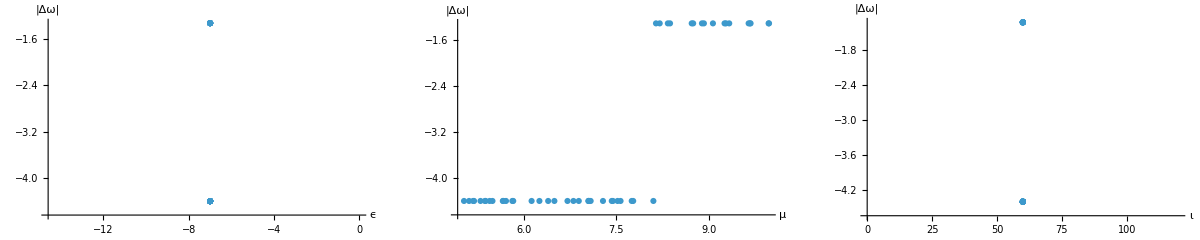

```mathematica
(* See "QNM_compute.nb" for the computation *)
data=Import["QNM_data\\Kerr_0_emidRdI_1.m"];
(*accept=Select[data,#[[-1]]<10^-7&];reject=Select[data,#[[-1]]>10^-3&];*)
label={"ϵ","μ","ι","ω","|Δω|"};scale={"Log10",None,None,None,"Log10"};

Print["Dim[data] = ",data//Dimensions(*,
"\tDim[accept] = ",accept//Dimensions,
"\tDim[reject] = ",reject//Dimensions*)];
Print["ϵ_(min/max) = ",{Min[data[[;;,1]]],Max[data[[;;,1]]]},
"\t μ_(min/max) = ",{Min[data[[;;,2]]],Max[data[[;;,2]]]},
"\t ι_(min/max) = ",{Min[data[[;;,3]]],Max[data[[;;,3]]]}];
```

Dim[data] = {100,5}

ϵ_(min/max) = {1.12124×10^-9,7.86647×10^-6}	 μ_(min/max) = {3.00017,6.99608}	 ι_(min/max) = {50.0045,69.886}

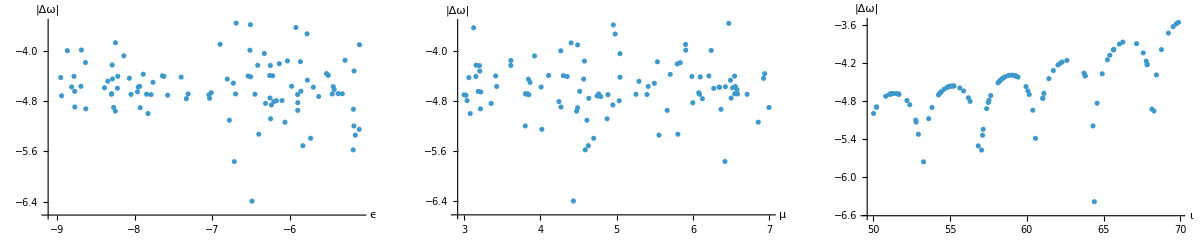

```mathematica
plots={};
Module[{index,l,s,point},
Do[index={i,-2};l=Extract[label,{{i},{-1}}];s=Extract[scale,{{i},{-1}}];
point={Extract[Abs[data],{;;,index}](*,Extract[accept,{;;,index}],Extract[reject,{;;,index}]*)};
AppendTo[plots,ListPlot[point,AxesLabel->l,ScalingFunctions->s,PlotRange->All]],
{i,3}]];

GraphicsGrid[{plots},ImageSize->Full]
```

## Parameter space

## General case V2

Operation to compute the series coefficients have been tested at low order, compute at higher order for following use of the integrator. Integrator waiting for test

```mathematica
(* Tortoise coordinate *)
rs[r_]:=Simplify[Integrate[(r^2+a^2)/((r-r1)(r-r2)),r]/.{r1->rp,r2->rm},{r>rp>0,a>0}];
rs[r]
```

r+(M-M/(√(1-χ^2))) Log[r+M (-1+√(1-χ^2))]+M (1+1/(√(1-χ^2))) Log[r-M (1+√(1-χ^2))]

```mathematica
(* Verify it satisfies its definition *)
Simplify[D[rs[r],r]]
```

(a^2+r^2)/(a^2-2 M r+r^2)

### Angular eigenvalues

```mathematica
ap=Max[Abs[m],Abs[s]];
am=(m s)/Max[Abs[m],Abs[s]];
h[l_]:=((l^2-ap^2)(l^2-am^2)(l^2-s^2))/(2(l-1/2)l^3(l+1/2));
fslm={l(l+1)−s(s+1),−2(m s^2)/(l(l+1)),h[l+1]−h[l]−1};(* see Eqs. 2.16 of https://arxiv.org/pdf/gr-qc/0511111 *)
Aslm=Simplify[Sum[fslm[[n]](a ω)^(n-1),{n,1,3}]];(* angular eigenvalues in the limit aω << 1 *)
λ=Aslm+(a ω)^2-2a ω m;
```

## Computing the QNMs

```mathematica
(* Potential from Eq. 4.2 of https://arxiv.org/pdf/0808.1615*)
K=(r^2+a^2)ω-a m;
G=(s(r-M))/(r^2+a^2)+(r Δ[r])/((r^2+a^2)^2);
V2=Simplify[(K^2-2ⅈ s(r-M)K+Δ[r](4ⅈ s ω r-Λ))/((r^2+a^2)^2)-G^2-Δ[r]/(r^2+a^2)D[G,r]](* where the last term is dG/dr_* in terms of r *)
EQ2=(Δ[r]/(r^2+a^2))^2 Y''[r]+Δ[r]/(r^2+a^2)D[Δ[r]/(r^2+a^2),r]Y'[r]+V2 Y[r];(* where Y[r]=Δ^(s/2)(r^2+a^2)^(1/2)R[r] *)
```

-1/((r^2+M^2 χ^2)^4)((r^3 (1+s)-M r^2 (2+s)-M^3 s χ^2+M^2 r (1+s) χ^2)^2+(-2 M r+r^2+M^2 χ^2) (-r^4 (1+s)+2 M r^3 (2+s)+2 M^3 r (-2+s) χ^2+M^4 (1+s) χ^4)-(r^2+M^2 χ^2)^2 ((-2 M r+r^2+M^2 χ^2) (-Λ+4 ⅈ r s ω)+(m M χ-(r^2+M^2 χ^2) ω)^2+2 ⅈ (M-r) s (-m M χ+(r^2+M^2 χ^2) ω)))

### Expansion at the horizon

```mathematica
Ω=a/(2M rp);
k=ω-m Ω;(* frequency near the horizon *)
```

```mathematica
Yhor[r_]:=Δ[r]^(s/2)(r^2+a^2)^(1/2)Δ[r]^-s Exp[-ⅈ k rs[r]];(* se la superficie è poco fuori l'orizzonte posso usare somma di entrante e uscente *)
Simplify[Series[Yhor[r],{r,rp,0}],{M>0,a>0}]
```

(-√(-a^2+M^2) (M+√(-a^2+M^2)-r))^(-s/2) (-M-√(-a^2+M^2)+r)^((ⅈ (a m-2 M (M+√(-a^2+M^2)) ω))/(2 √(-a^2+M^2))) (2^(1/2-s/2+(ⅈ a (m (-M+√(-a^2+M^2))+2 a M ω))/(-2 a^2+2 M (M+√(-a^2+M^2)))) ⅇ^(-(ⅈ (a^3 m-a m M (M+√(-a^2+M^2))+4 M^3 (M+√(-a^2+M^2)) ω-2 a^2 M (2 M+√(-a^2+M^2)) ω))/(2 M (-a^2+M (M+√(-a^2+M^2))))) (-a^2+M^2)^((ⅈ a (m (-M+√(-a^2+M^2))+2 a M ω))/(-4 a^2+4 M (M+√(-a^2+M^2)))) √(M (M+√(-a^2+M^2)))+O[r-M-√(-a^2+M^2)]^1)

```mathematica
Υ[r_]:=Exp[-ⅈ k rs[r]] Δ[r]^(-s/2)η[r];
S1=EQ2/.{Y[r]->Υ[r],Y'[r]->Υ'[r],Y''[r]->Υ''[r]};
CT1=Exp[-ⅈ k rs[r]] Δ[r]^(-s/2);
sHor=Simplify[S1/CT1,{M>0,a>0}]
```

-1/((a^2+r^2)^4)(2 (M-r)^2 (a^2+r^2)^2 s η[r]-2 r (-M+r) (a^2+r^2) (a^2+r (-2 M+r)) s η[r]+(a^2+r^2)^2 (a^2+r (-2 M+r)) s η[r]-(M-r)^2 (a^2+r^2)^2 s (2+s) η[r]+(a^2+r (-2 M+r)) (2 a^2 M r (-2+s)+a^4 (1+s)-r^4 (1+s)+2 M r^3 (2+s)) η[r]+(a^2 (r-M s+r s)+r^2 (r (1+s)-M (2+s)))^2 η[r]-(ⅈ (a^2-r^2) (a^2+r^2)^2 (a m-2 M (M+√(-a^2+M^2)) ω) η[r])/(M+√(-a^2+M^2))+(ⅈ r (a^2+r^2)^2 (a^2+r (-2 M+r))^2 (a m-2 M (M+√(-a^2+M^2)) ω) η[r])/(M (M+√(-a^2+M^2)) (M-√(-a^2+M^2)-r) (M+√(-a^2+M^2)-r))+((a^2+r^2)^4 (a^2+r (-2 M+r))^2 (a m-2 M (M+√(-a^2+M^2)) ω)^2 η[r])/(4 M^2 (M+√(-a^2+M^2))^2 (M+√(-a^2+M^2)-r)^2 (-M+√(-a^2+M^2)+r)^2)+(ⅈ (M-r) (-a^2+(2 M-r) r) (a^2+r^2)^3 (-a m+2 M (M+√(-a^2+M^2)) ω) η[r])/(M (M+√(-a^2+M^2)) (M-√(-a^2+M^2)-r) (M+√(-a^2+M^2)-r))-(ⅈ (M-r) (-a^2+(2 M-r) r) (a^2+r^2)^3 s (-a m+2 M (M+√(-a^2+M^2)) ω) η[r])/(M (M+√(-a^2+M^2)) (M-√(-a^2+M^2)-r) (M+√(-a^2+M^2)-r))+(a^2+r^2)^2 (-(a m-(a^2+r^2) ω)^2+2 ⅈ (-M+r) s (-a m+(a^2+r^2) ω)+(a^2+r (-2 M+r)) (Λ-4 ⅈ r s ω)) η[r]-(-2 M+2 r) (a^2+r^2)^2 (a^2+r (-2 M+r)) η'[r]+2 r (a^2+r^2) (a^2+r (-2 M+r))^2 η'[r]+(-2 M+2 r) (a^2+r^2)^2 (a^2+r (-2 M+r)) s η'[r]-(ⅈ (a^2+r^2)^3 (a^2+r (-2 M+r))^2 (a m-2 M (M+√(-a^2+M^2)) ω) η'[r])/(M (M+√(-a^2+M^2)) (M-√(-a^2+M^2)-r) (M+√(-a^2+M^2)-r))-(a^2+r^2)^2 (a^2+r (-2 M+r))^2 η''[r])

```mathematica
(* Series coefficients *)
CoefHor[ord_]:=Module[{Η,s1},
Η[r_]:=Sum[hHor[i](r-rp)^i,{i,0,ord+5}];
s1=Simplify[Series[sHor/.{η[r]->Η[r],η'[r]->D[Η[r],r],η''[r]->D[Η[r],{r,2}]},{r,rp,ord}],{M>0,a>0}];

(* Solve the system *)
Simplify[Solve[Table[SeriesCoefficient[s1,i]==0,{i,0,ord}],Table[hHor[i],{i,1,ord}]]]
]
```

```mathematica
ordHor=4;(* NOTE: the last coefficient is one order higher *)
coefHor=CoefHor[ordHor][[1]];
```

```mathematica
Export["CoefHor_4_Kerr.m",coefHor]
```

CoefHor_4_Kerr.m

### Expansion at infinity

```mathematica
Yinf[r_]:=Δ[r]^(s/2)(r^2+a^2)^(1/2)Exp[ⅈ ω rs[r]]/r^(2s+1);
Simplify[Series[Yinf[r],{r,∞,0}],{M>0,a>0}]
```

ⅇ^(ⅈ ω r+2 ⅈ M ω Log[r]-(4 ⅈ M^2 ω)/r+O[1/r]^2) r^(-2 s) (a^2+r (-2 M+r))^(s/2) (1+O[1/r]^2)

```mathematica
Υ[r_]:=Exp[ⅈ ω rs[r]] r^-s γ[r];
S2=EQ2/.{Y[r]->Υ[r],Y'[r]->Υ'[r],Y''[r]->Υ''[r]};
CT2=Exp[ⅈ ω rs[r]] r^-s;
sInf=Simplify[S2/CT2,{M>0,a>0}]
```

1/(r^2 (a^2+r^2)^4)((-2 a^7 m r^2 ω+a^8 s (1+s-2 ⅈ r ω)-2 a m r^6 (ⅈ M s+r (-ⅈ s+r ω))-2 a^5 m r^2 (ⅈ M s+r (-ⅈ s+3 r ω))-2 a^3 m r^4 (2 ⅈ M s+r (-2 ⅈ s+3 r ω))+a^6 r (-2 M s (1+2 s)-6 ⅈ r^2 s ω+r (-1+m^2+3 s+4 s^2-Λ+6 ⅈ M s ω))+r^6 (M^2 (4+8 s+3 s^2)-r^2 Λ+2 M r (-1-2 s-s^2+Λ-ⅈ r s ω))+a^2 r^4 (M^2 (-8+8 s+6 s^2)+2 M r (2-5 s-4 s^2+2 Λ+ⅈ r s ω)+r^2 (-1+m^2+s+2 s^2-3 Λ-2 ⅈ r s ω))+a^4 r^2 (3 M^2 s^2+2 M r (3-4 s-5 s^2+Λ+5 ⅈ r s ω)+r^2 (-2+2 m^2+3 s+5 s^2-3 Λ-6 ⅈ r s ω))) γ[r]+r (a^2+r^2) (a^2+r (-2 M+r)) (2 (-a^4 (s-ⅈ r ω)+r^3 (M+2 M s-r s+ⅈ r^2 ω)+a^2 r (-M+2 M s-2 r s+2 ⅈ r^2 ω)) γ'[r]+r (a^2+r^2) (a^2+r (-2 M+r)) γ''[r]))

```mathematica
(* Series coefficients *)
CoefInf[ord_]:=Module[{Γ,s1},
Γ[r_]:=Sum[gInf[i]/r^i,{i,0,ord+5}];
s1=Simplify[Series[sInf/.{γ[r]->Γ[r],γ'[r]->D[Γ[r],r],γ''[r]->D[Γ[r],{r,2}]},{r,∞,ord}],{M>0,a>0}];

(* Solve the system *)
Simplify[Solve[Table[SeriesCoefficient[s1,i]==0,{i,2,ord}],Table[gInf[i],{i,1,ord-1}]]]
]
```

```mathematica
ordInf=10;(* NOTE: the last coefficient is one order lower *)
coefInf=CoefInf[ordInf][[1]];
```

```mathematica
Export["CoefInf_10_Kerr.m",coefInf](* before set the directory *)
```

CoefInf_10_Kerr.m

### QNM finder

```mathematica
coefHor=Import["CoefHor_3_Kerr.m"];
coefInf=Import["CoefInf_10_Kerr.m"];
```

```mathematica
(* Integrator V1.5 - precision check implementation - to be tested *)
IntQNM[ω0_,χ0_,value_,coefHor_,coefInf_]:=Module[{rules,param,prec,rHor,rm,rInf,ξ,ξHor,ξInf,EQs,BCs,ordHor,ordInf},
rules={AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->20};(*,Method->"StiffnessSwitching"*)

param=Union[{M->1,ω->ω0,χ->χ0,hHor[0]->1,gInf[0]->1,l->2,m->2,s->-2,Λ->λ},Thread[{eps,match,inf}->value]];
prec=Max[20,Precision[param]];param=SetPrecision[param,prec];

rHor=rp(1+eps)//.param;
rm=match×M//.param;
rInf=inf×M//.param;

EQs=SetPrecision[{EQ2==0}//.Union[param,{Y[r]->ξ[r],Y'[r]->ξ'[r],Y''[r]->ξ''[r]}],prec];

(* Solution integrating from the horizon *)
ordHor=Length[coefHor];
ξHor=Exp[-ⅈ k rs[r]] Δ[r]^(-s/2)Sum[hHor[i] (r-rp)^i,{i,0,ordHor}]//.Union[param,coefHor];
BC1=SetPrecision[ξHor/.r->rHor,prec];BC2=SetPrecision[D[ξHor,r]/.r->rHor,prec];
BCs={ξ[rHor]==BC1,ξ'[rHor]==BC2};

Υhor=ξ[r]/.NDSolve[Union[EQs,BCs],ξ,{r,rHor,rm},rules][[1]];

(* Solution integration from infinity *)
ordInf=Length[coefInf];
ξInf=Exp[ⅈ ω rs[r]] r^-s Sum[gInf[i]/r^i,{i,0,ordInf}]//.Union[param,coefInf];
BC1=SetPrecision[ξInf/.r->rInf,prec];BC2=SetPrecision[D[ξInf,r]/.r->rInf,prec];
BCs={ξ[rInf]==BC1,ξ'[rInf]==BC2};

Υinf=ξ[r]/.NDSolve[Union[EQs,BCs],ξ,{r,rInf,rm},rules][[1]];

(*Linear combination*)
b=Υhor/Υinf/.r->rm;(* we fix the coefficients of the linear combination in order for ψn to be continuous at r=rm *)
Υn=Piecewise[{{Υhor,r<rm},{b×Υinf,r≥rm}}];
ΔΥp=(D[Υhor,r]-D[b Υinf,r])/D[Υhor,r]/.r->rm;
{ΔΥp}
]
```

```mathematica
IntQNM[37/100-88/1000 ⅈ,0,{10^-4,10,50},coefHor,coefInf]
```

{-0.0000479193256562+3.1945878495×10^-6 ⅈ}

```mathematica
FindQNM[ωguess_,χ0_]:=Module[{gg},
gg[xx_?NumericQ]:=IntQNM[xx,χ0,{10^-3,10,50},coefHor,coefInf][[1]];
root=xx/.FindRoot[gg[xx]==0,{xx,ωguess},AccuracyGoal->6,WorkingPrecision->20][[1]];
check=Abs[gg[root]];
{root,check}
]
```

```mathematica
ωfound=FindQNM[37/100-88/1000 ⅈ,0]
```

{0.37366174518717673096-0.088945884778164320764 ⅈ,1.×10^-15}

```mathematica
Abs[ωfound[[1]]-(0.373671-0.08896ⅈ)]
```

0.0000168787

### Past integrators

```mathematica
(* Integrator - to be tested *)
IntQNM[ω0_,a0_,value_,coefHor_,coefInf_]:=Module[{rules,param,rHor,rm,rInf,ξ,ξHor,ξInf,EQs,BCs,ordHor,ordInf},
rules={AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->20};(*,Method->"StiffnessSwitching"*)
param=Union[{M->1,ω->ω0,a->a0,hHor[0]->1,gInf[0]->1,l->2,m->2,s->-2,Λ->λ},Thread[{eps,match,inf}->value]];

rHor=rp(1+eps)//.param;
rm=match×M//.param;
rInf=inf×M//.param;

EQs=SetPrecision[{EQ2==0}//.Union[param,{Y[r]->ξ[r],Y'[r]->ξ'[r],Y''[r]->ξ''[r]}],20];

(* Solution integrating from the horizon *)
ordHor=Length[coefHor];
ξHor=SetPrecision[Exp[-ⅈ k rs[r]] Δ[r]^(-s/2)Sum[hHor[i] (r-rp)^i,{i,0,ordHor}]//.Union[param,coefHor],20];
BCs=SetPrecision[{ξ[rHor]==ξHor/.r->rHor,ξ'[rHor]==D[ξHor,r]/.r->rHor},20];
solHor=NDSolve[Union[EQs,BCs],ξ,{r,rHor,rm},rules];
Υhor=ξ[r]/.solHor[[1]];

(* Solution integration from infinity *)
ordInf=Length[coefInf];
ξInf=SetPrecision[Exp[ⅈ ω rs[r]] r^-s Sum[gInf[i]/r^i,{i,0,ordInf}]//.Union[param,coefInf],20];
BCs=SetPrecision[{ξ[rInf]==ξInf/.r->rInf,ξ'[rInf]==D[ξInf,r]/.r->rInf},20];
solInf=NDSolve[Union[EQs,BCs],ξ,{r,rInf,rm},rules];
Υinf=ξ[r]/.solInf[[1]];

(*Linear combination*)
b=Υhor/Υinf/.r->rm;(* we fix the coefficients of the linear combination in order for ψn to be continuous at r=rm *)
Υn=Piecewise[{{Υhor,r<rm},{b×Υinf,r≥rm}}];
ΔΥp=(D[Υhor,r]-D[b Υinf,r])/D[Υhor,r]/.r->rm;
{ΔΥp}
]
```

## Numerical Stability

### Spin

```mathematica
χarray={10^-2,5 10^-2,10^-1,15 10^-2,2 10^-1,25 10^-2,3 10^-1};
ωtrue={0.3749365685-0.08894183057ⅈ,0.3801455748-0.08884890191ⅈ,0.3870175384-0.08870569903ⅈ,0.3943329877-0.08852826817ⅈ,0.4021453242-0.08831116621ⅈ,0.4105179098-0.08804765025ⅈ,0.4195266818-0.08772927189ⅈ};
(*ωguess={};*)
```

```mathematica
ωfound={};
ωguess=0.4-0.1 ⅈ;
Monitor[Do[
AppendTo[ωfound,FindQNM[ωguess,χarray[[i]]][[1]]];ωguess=ωfound[[-1]],{i,1,Length[χarray]}
],ωfound]
```

```mathematica
Export["QNM_Kerr_generale.dat",ωfound]
```

QNM_Kerr_generale.dat

```mathematica
ωimport=Import["QNM_Kerr_generale.dat"]//ToExpression;
ωimport[[All,1]]
```

{0.37492448041496405795-0.088927383842179113597 ⅈ,0.38012871562853420118-0.088844746191951043439 ⅈ,0.38700480863123252224-0.088714593887673309863 ⅈ,0.39433255364106886758-0.088542402787696071729 ⅈ,0.40215601505885246292-0.088319456631938960877 ⅈ,0.41052985864583464943-0.088045516438116739603 ⅈ,0.41953134180241006431-0.087724027160154668552 ⅈ}

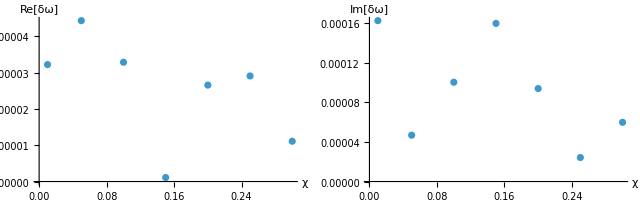

```mathematica
ΔωR=Abs[(Re[ωimport[[All,1]]]-Re[ωtrue])/Re[ωtrue]];(* Table[ωfound[[i]]-ωtrue[[i]],{i,1,size}]; *)
ΔωI=Abs[(Im[ωimport[[All,1]]]-Im[ωtrue])/Im[ωtrue]];
dataR=Transpose@{χarray,ΔωR};
dataI=Transpose@{χarray,ΔωI};

GraphicsRow[{ListPlot[dataR,AxesLabel->{"χ","Re[δω]"}],ListPlot[dataI,AxesLabel->{"χ","Im[δω]"}]}](* ,ScalingFunctions->{None,"Log"} *)
```

```mathematica
(* con ordHor=3
1.403173173208927*^-7-2.594252477838843*^-7 ⅈ,1.3839418633310174*^-7-2.5434630081255793*^-7 ⅈ,1.305543594343206*^-7-2.399207012504512*^-7 ⅈ *)
```

```mathematica
(* con ordHor=7
1.403173173208927*^-7-2.594252477838843*^-7 ⅈ,1.3839418633310174*^-7-2.5434630081255793*^-7 ⅈ,1.305543594343206*^-7-2.399207012504512*^-7 ⅈ *)
```

```mathematica
(*ωR=Re[ωimport[[All,1]]]/Re[ωtrue];(* Table[ωfound[[i]]-ωtrue[[i]],{i,1,size}]; *)
ωI=Im[ωimport[[All,1]]]/Im[ωtrue];*)
ωR=Re[ωfound]/Re[ωtrue];(* Table[ωfound[[i]]-ωtrue[[i]],{i,1,size}]; *)
ωI=Im[ωfound]/Im[ωtrue];
dataR=Transpose@{χarray,ωR};
dataI=Transpose@{χarray,ωI};

GraphicsRow[{ListPlot[dataR,AxesLabel->{"χ","ω_R/ω_R^Kerr"}],ListPlot[dataI,AxesLabel->{"χ","ω_I/ω_I^Kerr"}]}](* ,ScalingFunctions->{None,"Log"} *)
```

-Graphics-